```mathematica
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
f[x_]:=a x^2+b x+c;
```

```mathematica
ExpData={{{-8,-220},ErrorBar[10]},{{-7,-148},ErrorBar[10]},{{-6,-100},ErrorBar[10]},{{-5,-45},ErrorBar[10]},{{-4,-6},ErrorBar[10]},{{-3,20},ErrorBar[10]},{{-2,55},ErrorBar[10]},{{-1,78},ErrorBar[10]},{{0,106},ErrorBar[10]},{{1,115},ErrorBar[10]},{{2,125},ErrorBar[10]},{{3,125},ErrorBar[10]},{{4,115},ErrorBar[10]},{{5,108},ErrorBar[10]},{{6,78},ErrorBar[10]},{{7,50},ErrorBar[10]},{{8,20},ErrorBar[10]},{{9,-5},ErrorBar[10]},{{10,-45},ErrorBar[10]},{{11,-95},ErrorBar[10]},{{12,-150},ErrorBar[10]},{{13,-220},ErrorBar[10]}};
```

```mathematica
DataPoints=22;NumOfParas=3;dof=DataPoints-NumOfParas;
```

```mathematica
Link=LinkCreate["QuadraticFunctionFit",LinkProtocol->"SharedMemory",LinkMode->Listen];
```

```mathematica
LinkWrite[Link,NumOfParas];LinkWrite[Link,dof];
```

```mathematica
Counter=0;
```

```mathematica
While[Links["QuadraticFunctionFit"]!={},Counter=Counter+1;
{a,b,c}=LinkRead[Link];
chiSqure=Sum[(f[ExpData[[i,1,1]]]-ExpData[[i,1,2]])^2/10^2,{i,1,22}];
Print["a=",a,"   ","b=",b,"   ","c=",c,"      ","\!\(\*SuperscriptBox[\(χ\), \(2\)]\)/d.o.f=",chiSqure/dof,"   ","计算进度为：",Counter];
LinkWrite[Link,chiSqure];]
```

a=1.   b=1.   c=1.      χ^2/d.o.f=292.089   计算进度为：1

a=1.03638   b=1.   c=1.      χ^2/d.o.f=299.589   计算进度为：2

a=0.963622   b=1.   c=1.      χ^2/d.o.f=284.725   计算进度为：3

a=1.00364   b=1.   c=1.      χ^2/d.o.f=292.833   计算进度为：4

a=0.996362   b=1.   c=1.      χ^2/d.o.f=291.346   计算进度为：5

a=1.   b=1.03638   c=1.      χ^2/d.o.f=292.402   计算进度为：6

a=1.   b=0.963622   c=1.      χ^2/d.o.f=291.778   计算进度为：7

a=1.   b=1.01137   c=1.      χ^2/d.o.f=292.187   计算进度为：8

a=1.   b=0.988626   c=1.      χ^2/d.o.f=291.991   计算进度为：9

a=1.   b=1.   c=1.03638      χ^2/d.o.f=292.133   计算进度为：10

a=1.   b=1.   c=0.963622      χ^2/d.o.f=292.045   计算进度为：11

a=1.   b=1.   c=1.07756      χ^2/d.o.f=292.182   计算进度为：12

a=1.   b=1.   c=0.922441      χ^2/d.o.f=291.996   计算进度为：13

a=-0.979621   b=-6.96481   c=-50.7727      χ^2/d.o.f=274.845   计算进度为：14

a=-0.0227867   b=-3.11508   c=-25.7488      χ^2/d.o.f=153.927   计算进度为：15

a=-0.0219433   b=-3.11508   c=-25.7488      χ^2/d.o.f=153.961   计算进度为：16

a=-0.0236302   b=-3.11508   c=-25.7488      χ^2/d.o.f=153.894   计算进度为：17

a=-0.0227867   b=-3.10682   c=-25.7488      χ^2/d.o.f=153.887   计算进度为：18

a=-0.0227867   b=-3.12334   c=-25.7488      χ^2/d.o.f=153.968   计算进度为：19

a=-0.0227867   b=-3.11508   c=-25.6925      χ^2/d.o.f=153.885   计算进度为：20

a=-0.0227867   b=-3.11508   c=-25.8051      χ^2/d.o.f=153.97   计算进度为：21

a=-0.574766   b=0.140951   c=-1.80488      χ^2/d.o.f=102.926   计算进度为：22

a=-2.78268   b=13.1651   c=93.9707      χ^2/d.o.f=1.62745   计算进度为：23

a=-3.03972   b=14.6813   c=105.121      χ^2/d.o.f=0.513826   计算进度为：24

a=-3.03964   b=14.6813   c=105.121      χ^2/d.o.f=0.513835   计算进度为：25

a=-3.03981   b=14.6813   c=105.121      χ^2/d.o.f=0.513818   计算进度为：26

a=-3.03967   b=14.6813   c=105.121      χ^2/d.o.f=0.513832   计算进度为：27

a=-3.03977   b=14.6813   c=105.121      χ^2/d.o.f=0.513821   计算进度为：28

a=-3.03972   b=14.6821   c=105.121      χ^2/d.o.f=0.513525   计算进度为：29

a=-3.03972   b=14.6805   c=105.121      χ^2/d.o.f=0.514128   计算进度为：30

a=-3.03972   b=14.6818   c=105.121      χ^2/d.o.f=0.513643   计算进度为：31

a=-3.03972   b=14.6808   c=105.121      χ^2/d.o.f=0.514009   计算进度为：32

a=-3.03972   b=14.6813   c=105.126      χ^2/d.o.f=0.51412   计算进度为：33

a=-3.03972   b=14.6813   c=105.115      χ^2/d.o.f=0.513533   计算进度为：34

a=-3.03972   b=14.6813   c=105.124      χ^2/d.o.f=0.514004   计算进度为：35

a=-3.03972   b=14.6813   c=105.117      χ^2/d.o.f=0.513648   计算进度为：36

a=-3.04312   b=15.0343   c=102.974      χ^2/d.o.f=0.348959   计算进度为：37

a=-3.0451   b=15.2396   c=101.725      χ^2/d.o.f=0.323183   计算进度为：38

a=-3.04506   b=15.2396   c=101.725      χ^2/d.o.f=0.323183   计算进度为：39

a=-3.04514   b=15.2396   c=101.725      χ^2/d.o.f=0.323183   计算进度为：40

a=-3.0451   b=15.24   c=101.725      χ^2/d.o.f=0.323183   计算进度为：41

a=-3.0451   b=15.2392   c=101.725      χ^2/d.o.f=0.323183   计算进度为：42

a=-3.0451   b=15.2396   c=101.728      χ^2/d.o.f=0.323183   计算进度为：43

a=-3.0451   b=15.2396   c=101.723      χ^2/d.o.f=0.323183   计算进度为：44

LinkObject::linkd: Unable to communicate with closed link LinkObject[QuadraticFunctionFit,520,10].

Set::shape: Lists {a,b,c} and $Failed are not the same shape.

a=-3.0451   b=15.2396   c=101.723      χ^2/d.o.f=0.323183   计算进度为：45

LinkObject::linkn: Argument LinkObject[QuadraticFunctionFit,520,10] in LinkWrite[LinkObject[QuadraticFunctionFit,520,10],6.14047] has an invalid LinkObject number; the link may be closed.

```mathematica
LinkClose[Link];
```

LinkObject::linkn: Argument LinkObject[QuadraticFunctionFit,520,10] in LinkClose[LinkObject[QuadraticFunctionFit,520,10]] has an invalid LinkObject number; the link may be closed.

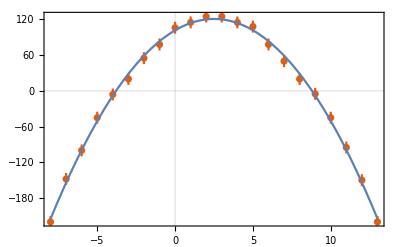

```mathematica
ExpPlot=ErrorListPlot[ExpData,PlotTheme->"Scientific"];
ModelPlot=Plot[-3.0451 x^2+15.2396 x+101.7254,{x,-8,13}];
Show[ExpPlot,ModelPlot]
```